```mathematica
(* This notebook gives the energies of a three body system in a harmonic trap interacting only with a three-body contact interaction.
```

{E3→3.27595}

```mathematica
Clear[b3];
E3=6.6276242612330165;
FindRoot[1/b3-(1/128 π(E3+1)(2(E3-1)HarmonicNumber[1/2-E3/2]+E3+3)),{b3,0.51}]
```

{b3→19254.6}

```mathematica
Clear[E3];
b3=0.04434250561677464;
b3=-1;
FindRoot[1/b3-(1/128 π(E3+1)(2(E3-1)HarmonicNumber[1/2-E3/2]+E3+3)),{E3,6.01}]
```

{E3→6.45818}

```mathematica
Energies={};
Clear[E3,b3];
(*b3=0.04434250561677464;*)
For[b3=-1,b3≤1,b3+=1,
If[Abs[b3]≤10^-3,b3+=.1];
EnergiesTemp={};
For[i=-1/Sqrt[2],i≤10,i+=.2/Sqrt[3],
If[Abs[Mod[i,2]-1]≤10^-2,Print[i];i+=.2/Sqrt[3];Print[i]];
AppendTo[EnergiesTemp,FindRoot[1/b3-(1/128 π(E3+1)(2(E3-1)HarmonicNumber[1/2-E3/2]+E3+3)),{E3,i},MaxIterations->1000]];];  
EnergiesTemp=Union[EnergiesTemp,SameTest->(ReplaceAll[E3,#1]-ReplaceAll[E3,#2]≤.01&)];
For[i=1,i≤Length[EnergiesTemp],i++,AppendTo[Energies,{b3,ReplaceAll[E3,EnergiesTemp[[i]]]}]]];
Energies
```

8.99238

9.10785

8.99238

9.10785

{{-1,-1.},{-1,-0.757381},{-1,2.63175},{-1,4.48103},{-1,6.45818},{-1,8.46464},{-1,10.477},{0.1,-8.94652},{0.1,1.},{0.1,3.08902},{0.1,5.33835},{0.1,7.813},{0.1,10.1398},{0.1,12.2895},{0.1,14.3693},{0.1,16.4184},{0.1,18.4519}}

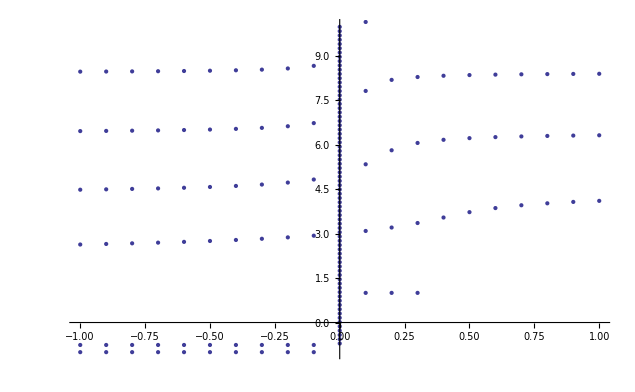

```mathematica
ListPlot[Energies,PlotRange->{-1,10}]
```